```mathematica
Table[If[IGSubisomorphicQ[CompleteGraph[4],First[s]],1,0],{k,allGraphs4AtomKeys},{l,allGraphs5AtomKeys}]
```

```mathematica
tetra=Select[possible,IGSubisomorphicQ[CompleteGraph[4],First[#]]&];
```

```mathematica
Length[tetra]
```

513

```mathematica
Table[With[{vals=Map[IGSubisomorphicQ[CompleteGraph[{3,3}],#]&,s]},{Fold[And,vals],Fold[Or,vals]}]
,{s,Take[tetra,50]           }]
```

{{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,True},{False,True},{False,True},{False,True},{False,True},{False,True},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,True},{False,True},{False,True},{False,True},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{False,False},{True,True},{True,True},{True,True},{False,True},{True,True},{True,True},{False,True},{False,True},{False,False},{True,True},{False,True},{False,True},{False,False},{False,True},{False,False},{False,True},{False,True}}

```mathematica
? IGSubisomorphicQ
```

IGSubisomorphicQ[subgraph, graph] tests if subgraph is contained within graph.

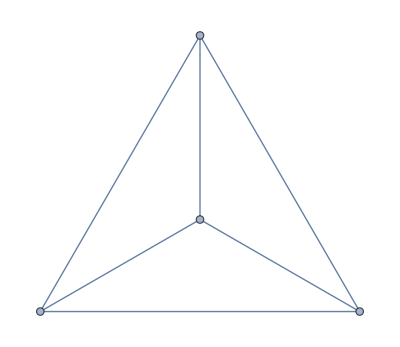

```mathematica
CompleteGraph[4]
```

```mathematica
Map[Labeled[Graph[#,GraphLayout->"CircularEmbedding",VertexStyle->Red,ImageSize->100],
{IGVF2SubisomorphismCount[CompleteGraph[{3,3}],#],IGVF2SubisomorphismCount[CompleteGraph[4],#]}]&,tetra[[8]]]
```

{-Graphics-{72,72},-Graphics-{72,72},-Graphics-{72,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{72,72},-Graphics-{0,72},-Graphics-{72,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{72,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{0,72},-Graphics-{72,72},-Graphics-{0,72},-Graphics-{0,72}}

```mathematica
ChromaticPolynomial[WheelGraph[5],x]//CompleteBaseCoeff
```

{0,0,0,1,2,1}

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]//CompleteBaseCoeff
```

{0,0,0,0,1}